A numerical test that to get an unbias estimator for the variance using a sample of N numbers we need to compute
varianceestimator = 1/(N-1)(Σ_i(x_i-av))^2
where  av = 1/N Σ_i x_i.

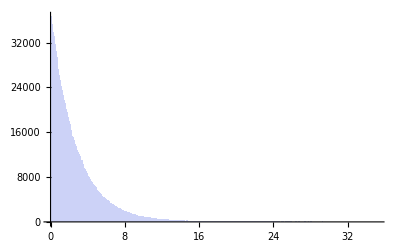

Mean of the variance computed over all trials: 2.66896

```mathematica
(* We generate n=3 numbers from a Gaussian distribution with σ^2=4 and compute the variance using the biased definition. We repeat this ntrials=100000 and take the average of the results. The average is different from 4 due to the bias *)
Block[{n=3,ntrials=1000000,data,res},
data=Partition[RandomVariate[NormalDistribution[0,2],n*ntrials],3];
res=Table[m=Mean[l];Total[(l-m)^2]/(n),{l,data}];
Print@Histogram[res];
Print["Mean of the variance computed over all trials: ",Mean[res]]
]
```

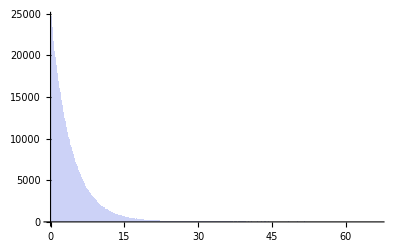

Mean of the variance computed over all trials: 4.00204

```mathematica
(* We generate n=3 numbers from a Gaussian distribution with σ^2=4 and compute the variance using the unbiased definition. We repeat this ntrials=100000 and take the average of the results. The average in this case is 4. *)
Block[{n=3,ntrials=1000000,data,res},
data=Partition[RandomVariate[NormalDistribution[0,2],n*ntrials],3];
res=Table[m=Mean[l];Total[(l-m)^2]/(n-1),{l,data}];
Print@Histogram[res];
Print["Mean of the variance computed over all trials: ",Mean[res]]
]
```